```mathematica
Clear[F,G,p,R,Cost];
F[a_,r_,μ_]:=F[a,r,μ]=Piecewise[{{1-∑_(i=0)^(r-1) 1/(i!)*(a/μ)^i*Exp[-a/μ], a>0}, {0, a==0}}];
p[a_,k_,j_,μ_]:=p[a,k,j,μ]=Piecewise[{{Boole[j==1], k==0}, {F[a,k,μ], k≥1&&j==1}, {F[a,k-j+1,μ]-F[a,k-j+2,μ], k≥1&&2≤j&&j≤k}, {1-F[a,1,μ], k≥1&&j==(k+1)}}];
G[a_,r_,μ_]:=G[a,r,μ]=Piecewise[{{μ*r*F[a,r+1,μ]/F[a,r,μ], a>0}, {0, a==0}}];
R[a_,k_,j_,γ_,μ_]:=R[a,k,j,γ,μ]=Piecewise[{{γ*a, (k==0||k==1)}, {(1-γ)*(G[a,k,μ]*(k-1))/2+γ*a, k≥2&&j==1}, {(1-γ)*(a*(j-2)+(G[a,k-(j-1),μ]*(k-(j-2)))/2)+γ*a, k≥2&&2≤j&&j≤k}, {(1-γ)*a*(j-2)+γ*a, k≥2&&j==(k+1)}}];
Cost[a_,n_,k_,γ_,μ_]:=Cost[a,n,k,γ,μ]=∑_(j=1)^(k+1) p[a,k,j,μ]*(R[a,k,j,γ,μ]+OptimalCost[n-1,j,γ,μ]);
```

```mathematica
Clear[PossiblePolicies];
PossiblePolicies[n_,k_,γ_,μ_]:=PossiblePolicies[n,k,γ,μ]=Module[{sol,result},
sol=NSolve[D[Cost[a,n,k,γ,μ],a]==0&&a>0,a]//Quiet;
If[Length[sol]==0,
result={0},
result=Flatten[{0,a/.sol}];
];
result
];
```

```mathematica
Clear[OptimalPolicy];
OptimalPolicy[n_,k_,γ_,μ_]:=OptimalPolicy[n,k,γ,μ]=Module[{a, costMin,i,result},
a=PossiblePolicies[n,k,γ,μ];
costMin=Min[Table[Cost[a[[i]],n,k,γ,μ],{i,1,Length[a]}]];
For[i=1,i≤Length[a],i++,
If[Cost[a[[i]],n,k,γ,μ]==costMin,
result=a[[i]];
];
];
result
];
```

```mathematica
Clear[OptimalCost];
OptimalCost[n_,k_,γ_,μ_]:=OptimalCost[n,k,γ,μ]=Piecewise[{{(1-γ)*(μ*k*(k-1))/2+γ*k*μ, n==0}, {Cost[OptimalPolicy[n,k,γ,μ],n,k,γ,μ], n≥1}}];
```

```mathematica
Cost[a,1,1,γ,μ]//FullSimplify
```

Piecewise[{{μ+γ (a+μ), a≤0}, {a γ+(ⅇ^(-a/μ)+γ) μ, True}}]

```mathematica
μ=1;
γ=0.5;
```

```mathematica
OptimalPolicy[1,1,γ,μ]==-μ*Log[γ]
```

True

```mathematica
num=4;
Table[OptimalCost[n,0,γ,μ],{n,0,num}]
Table[Table[If[n+k≤num,OptimalCost[n,k,γ,μ],0],{k,0,num}],{n,0,num}]//MatrixForm
Table[Table[If[n+k≤num,OptimalPolicy[n,k,γ,μ],0],{k,0,num}],{n,1,num}]//MatrixForm
```

{0.,0.5,1.34657,2.26002,3.17509}

(0. | 0.5 | 1.5 | 3. | 5.
0.5 | 1.34657 | 2.48969 | 4.02475 | 0
1.34657 | 2.26002 | 3.40683 | 0 | 0
2.26002 | 3.17509 | 0 | 0 | 0
3.17509 | 0 | 0 | 0 | 0)

(0 | 0.693147 | 1.75711 | 2.82577 | 0
0 | 0.826902 | 1.90223 | 0 | 0
0 | 0.83013 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

```mathematica
TeXForm[MatrixForm[Table[Table[If[n+k≤num,OptimalCost[n,k,γ,μ],0],{k,0,num}],{n,0,num}]]]
```

\left(
\begin{array}{ccccc}
 0. & 0.5 & 1.5 & 3. & 5. \\
 0.5 & 1.34657 & 2.48969 & 4.02475 & 0 \\
 1.34657 & 2.26002 & 3.40683 & 0 & 0 \\
 2.26002 & 3.17509 & 0 & 0 & 0 \\
 3.17509 & 0 & 0 & 0 & 0 \\
\end{array}
\right)

```mathematica
TeXForm[MatrixForm[Table[Table[If[n+k≤num,OptimalPolicy[n,k,γ,μ],0],{k,0,num}],{n,1,num}]]]
```

\left(
\begin{array}{ccccc}
 0 & 0.693147 & 1.75711 & 2.82577 & 0 \\
 0 & 0.826902 & 1.90223 & 0 & 0 \\
 0 & 0.83013 & 0 & 0 & 0 \\
 0 & 0 & 0 & 0 & 0 \\
\end{array}
\right)

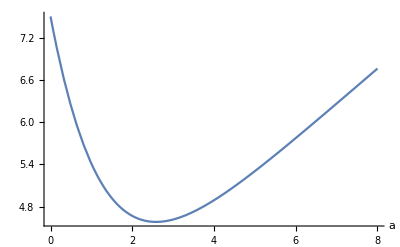

```mathematica
Plot[Cost[a,3,2,γ,μ],{a,0,8},AxesLabel->Automatic]
```

```mathematica
Cost[a,3,2,γ,μ]//FullSimplify
```

Piecewise[{{7.5+1. a, a≤0}, {2.76002+0.5 a+(4.73998+(1.64681+0.25 a) a) ⅇ^-a-(0.5 a^2)/(-1.+1. ⅇ^a), True}}]

```mathematica
TeXForm[FullSimplify[Cost[a,3,2,γ,μ]]]
```

\begin{cases}
 1. a+7.5 & a\leq 0 \\
 -\frac{0.5 a^2}{1. e^a-1.}+0.5 a+((0.25 a+1.64681) a+4.73998) e^{-a}+2.76002 & \text{True}
\end{cases}

```mathematica
PossiblePolicies[3,2,γ,μ]
OptimalPolicy[3,2,γ,μ]
OptimalCost[3,2,γ,μ]
```

{0,2.58223}

2.58223

4.58436

```mathematica
PossiblePolicies[3,2,γ,μ][[Ordering[Table[Cost[PossiblePolicies[3,2,γ,μ][[i]],3,2,γ,μ],{i,1,Length[PossiblePolicies[3,2,γ,μ]]}],1][[1]]]]
```

2.58223